```mathematica
eigenvalue equation
```

```mathematica
chartheta[x_,f_,theta_]=1/(12 f (-4+3 f^2))(2 f x (52-22 √(4-3 f^2)-24 x^2+3 f^2 (-13+6 x^2))+3 (-8 (-2+√(4-3 f^2)) (-5+2 x^2)+f^2 (60-17 √(4-3 f^2)+4 (-6+5 √(4-3 f^2)) x^2)) Cos[theta]-18 f (-4+3 f^2+2 √(4-3 f^2)) x Cos[2 theta]+3 (-3 f^2 (-4+√(4-3 f^2))+8 (-2+√(4-3 f^2))) Cos[3 theta])
TeXForm[chartheta[lambda,f,theta]]
```

```mathematica
Cterm[f_,theta_]          =Simplify[chartheta[0,f,theta]]
Btermx[x_,f_,theta_]=Simplify[(chartheta[x,f,theta]-Cterm[f,theta])/x]
Bterm[f_,theta_]          =Simplify[Btermx[0,f,theta]]
Atermx[x_,f_,theta_]=Simplify[(Btermx[x,f,theta]-Bterm[f,theta])/x]
Aterm[f_,theta_]          =Simplify[Atermx[0,f,theta]]
```

```mathematica
kai1[f_,theta_]=-Aterm[f,theta]/3+(-Qterm[f,theta]+Sqrt[Qterm[f,theta]^2+Pterm[f,theta]])^(1/3)+(-Qterm[f,theta]-Sqrt[Qterm[f,theta]^2+Pterm[f,theta]])^(1/3)
kai2[f_,theta_]=-Aterm[f,theta]/3+w2*(-Qterm[f,theta]+ⅈ*Sqrt[-(Qterm[f,theta]^2+Pterm[f,theta])])^(1/3)+w3*(-Qterm[f,theta]-ⅈ*Sqrt[-(Qterm[f,theta]^2+Pterm[f,theta])])^(1/3)
kai3[f_,theta_]=-Aterm[f,theta]/3+w3*(-Qterm[f,theta]+ⅈ*Sqrt[-(Qterm[f,theta]^2+Pterm[f,theta])])^(1/3)+w2*(-Qterm[f,theta]-ⅈ*Sqrt[-(Qterm[f,theta]^2+Pterm[f,theta])])^(1/3)
```

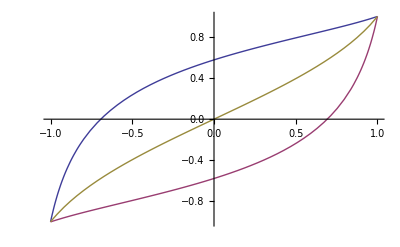

```mathematica
Plot[{kai1[f,0],kai2[f,0],kai3[f,0]},{f,-1,1}]
```

```mathematica
Plot3D[{Qterm[f,theta]^2+Pterm[f,theta]},{f,-1,1},{theta,0,Pi}]
```

-Graphics3D-

```mathematica
Plot3D[{kai1[f,theta],kai2[f,theta],kai3[f,theta]},{f,-1,1},{theta,0,Pi}]
```

-Graphics3D-

```mathematica
Plot3D[{kai1[f,theta*Pi],kai2[f,theta*Pi]},{f,-1,1},{theta,0,1},AxesLabel -> {f,θ/π}]
Export["m1general.eps",%]
```

-Graphics3D-

m1general.eps

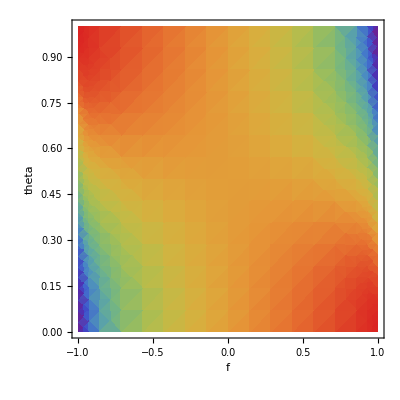

```mathematica
DensityPlot[{kai1[f,Pi*theta]},{f,-1,1},{theta,0,1},ColorFunction->ColorData["Rainbow"] ,PlotRange->{-1,1},AxesLabel -> {f,theta}]
```

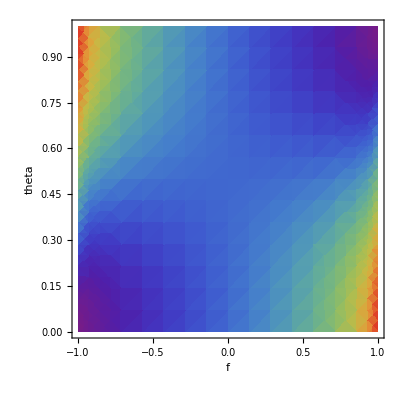

```mathematica
DensityPlot[{kai2[f,Pi*theta]},{f,-1,1},{theta,0,1},ColorFunction->ColorData["Rainbow"] ,PlotRange->{-1,1},AxesLabel -> {f,theta}]
```

```mathematica
fnmax=2
tnmax=2
Export["cp.dat",Table[N[Re[Limit[kai1[f,j*Pi/tnmax],f->i/fnmax]]],{i,-fnmax,fnmax},{j,0,tnmax}]]
Export["cm.dat",Table[N[Re[Limit[kai2[f,j*Pi/tnmax],f->i/fnmax]]],{i,-fnmax,fnmax},{j,0,tnmax}]]
```

2

2

cp.dat

cm.dat

cmp.dat